```mathematica
<<RLBot`
```

```mathematica
EulerAngleRotation[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\unit_tests

```mathematica
Det[({{0, 0, -1}, {0, -1, 0}, {-1, 0, 0}})]
```

1

```mathematica
4096 - 17
```

4079

```mathematica
input = <|
"car"-><|
"x"->{4079, 0,1400},
"v"->{0,0, -400},
"o"->({{0, 0, -1}, {0, -1, 0}, {-1, 0, 0}})
|>,
"dest"->{4079, 0,400},
"tangent" -> Normalize[{0, 0, -1}],
"time"->4.0,
"speed"->1000,
"offset"->100
|>;

Export["input.json", input];

RunProcess[{"bash","-c","../../../build_mingw/bin/pathing_test.exe input.json output.json"}]

data =Association[Import["output.json"]];
```

<|ExitCode→0,StandardOutput→Initializing rlutilities...\r
0x639c0000\r
setting mode: soccar\r
source: 4079.45, 0, 1400.03\r
car close to: 4079, 0, 1407.88 facing 0.0574957, 0, -0.998346\r
source_node: 8762 source_direction: 0 source_id: 140192\r
sssp time: 10.9712ms\r
dest close to: 4079, 0, 512 facing 0, -8.74228e-08, -1\r
destination_node: 3593 destination_direction: 8 dest_id: 57496\r
a = 1563.1 calculating error: -3791.19\r
a = -3500 calculating error: 7133.45\r
a = -193.956 calculating error: -1682.52\r
a = -1595.91 calculating error: 2055.97\r
a = -824.91 calculating error: -0.000244141\r
,StandardError→|>

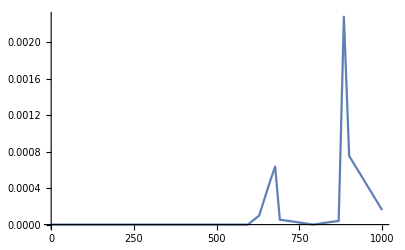

```mathematica
path = Association[data["path"]];
distances = path["distances"];
points = path["points"];
follow = Association[data["follow"]];
tplan = follow["plan"][[1, All, 1]];
splan = follow["plan"][[1, All, 2, 1]];
vplan = follow["plan"][[1, All, 2,2]];
ListLinePlot[Transpose[{path["distances"],path["curvatures"]}], PlotRange->All]
ListLinePlot[{
Transpose[{path["distances"],path["max_speeds"]}],
Transpose[{splan,vplan}]
}]
Graphics3D[{
Line[path["points"]]
}, Boxed->False]
```

```mathematica
dv =
```

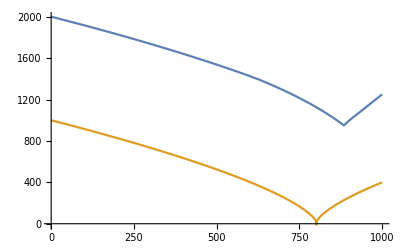

-Graphics3D-

```mathematica
Differences[
```

```mathematica
nodes = BinaryReadList["C:\\Users\\sam\\Documents\\GitHub\\RLUtilities\\assets\\soccar\\soccar_navigation_nodes.bin", {"Real32", "Real32", "Real32"}]
```

```mathematica
normals = BinaryReadList["C:\\Users\\sam\\Documents\\GitHub\\RLUtilities\\assets\\soccar\\soccar_navigation_normals.bin", {"Real32", "Real32", "Real32"}]
```

{{0.543019,0.624246,0.561647},{0.450077,0.450105,0.771256},{0.515814,0.49354,0.700253},12110,{-0.295987,-0.295987,-0.908176},{-0.253252,-0.253252,-0.933663}}
 |  |  |  |

```mathematica
normals[[8763]]
```

{-0.998346,0.,-0.0574957}

```mathematica
0.05749567970633507* 200
```

11.4991

```mathematica
Nearest[nodes, {4079, 0,1400}]
```

{{4079.,0.,1407.88}}

```mathematica
Position[nodes, Nearest[nodes, {4079, 0,1400}][[1]]]
```

{{8763}}

```mathematica
Length[path["points"]]
```

35

```mathematica
S = 1/2 SparseArray[{
Band[{1, 1}]->0,
Band[{3, 1}]->1,
Band[{1, 3}]->1
}, {Length[points], Length[points]+2}];
S[[{1,2, -2, -1}]] = IdentityMatrix[Length[points]+2][[{1,2,-2, -1}]];
```

```mathematica
smoothed = S.Join[{points[[1]]}, points, {points[[-1]]}]
```

{{0.,3000.,17.},{0.,3000.,17.},{-290.86,2999.41,17.},{-311.15,2998.13,17.},{-581.33,2996.73,17.},154,{-16.2801,397.805,17.},{-10.1376,431.775,17.},{0.,1000.,17.},{0.,1000.,17.}}
 |  |  |  |

```mathematica
Graphics3D[{
Red,
Line[smoothed],
Blue,
Line[points]
}]
```

-Graphics3D-

```mathematica
Join[{points[[1]]}, points, {points[[-1]]}]
```

{{0.,3000.,17.},{0.,3000.,17.},{-499.999,3000.8,17.},{-540.947,3000.33,17.},{-581.721,2998.82,17.},155,{-5.21065,431.53,17.},{-1.32054,465.731,17.},{0.,500.,17.},{0.,1000.,17.},{0.,1000.,17.}}
 |  |  |  |

```mathematica
γ=Interpolation[Table[{distances[[i]], points[[i]]}, {i, 1, Length[distances]}], InterpolationOrder->2];
γ2=Interpolation[Table[{distances[[i]], smoothed[[i]]}, {i, 1, Length[distances]}], InterpolationOrder->2];
```

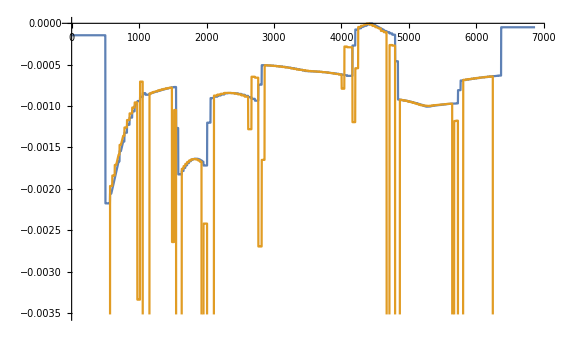

```mathematica
Plot[{-Norm[γ''[s]], -Norm[γ2''[s]]}, {s, 0, 6870}]
```

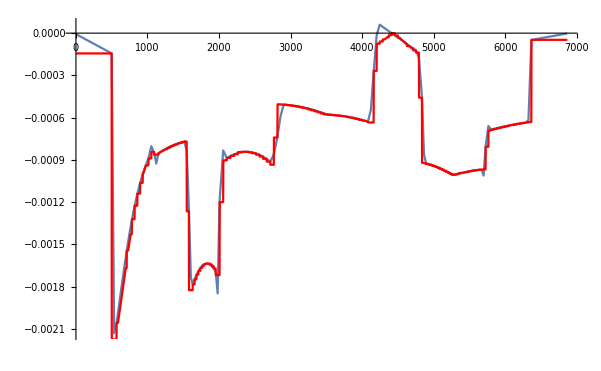

```mathematica
Show[
ListLinePlot[Transpose[{path["distances"],path["curvatures"]}], PlotRange->All],
Plot[-Norm[γ''[s]], {s, 0, 6870}, PlotStyle->Red]
]
```